## Fig8

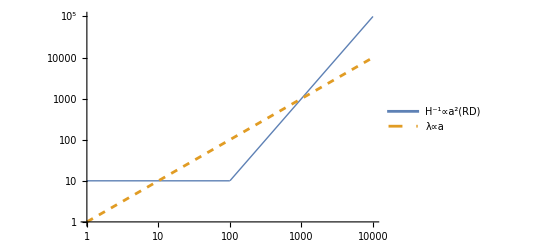

```mathematica
Hr[a_]:=Piecewise[{{10,a<=100},{10*(a/100)^2,a>100}}];
λ[a_]:=a;  
LogLogPlot[{Hr[a],λ[a]},{a,1,10000},PlotStyle->{Thick,Dashed},PlotLegends->{"H^-1∝a^2(RD)","λ∝a"}]
```